# Setting

```mathematica
Options[plotGrid]={ImagePadding->45};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

# High/Low temperature

## Sx dynamics

```mathematica
SxHamfixhJSpinSetsHighLowOld[flist_,TinJlist_,hinJlist_,Jbarstr_,beginSteplist_,endSteplist_,dir_,showfit_,nt_,stdJ_,plotdown_,plotup_,plotleft_,plotright_,fontsize_,loworhigh_]:=(
setlen=Length[hinJlist];
Tliststr=Table[StringReplace[If[FractionalPart[TinJlist[[i]]]!=0.,ToString[TinJlist[[i]]],ToString[NumberForm[TinJlist[[i]],{3,1}]]],"."->"_"],{i,1,setlen}];
hinJliststr=Table[StringReplace[If[FractionalPart[hinJlist[[i]]]!=0.,ToString[hinJlist[[i]]],ToString[NumberForm[hinJlist[[i]],{3,1}]]],"."->"_"],{i,1,setlen}];
(*Jbarstr=StringReplace[ToString[NumberForm[Jbar,{2,2}]],"."->"_"]*)
(*Δt=Λtscale/nt//N;*)
ΔtJlist=Table[Δt=Import[StringJoin[NotebookDirectory[],dir,"/","set_",ToString[i],"/Jbar"<>Jbarstr<>"/deltaT.csv"]];
Δt[[1,1]]
,{i,1,setlen}];
ΔtJlist=ΔtJlist/stdJ; (*assume stdJ=1*)
(*Print[ΔtJlist];*)
centerPt=(nt+1);
Sxlist=Table[Sx=Import[StringJoin[NotebookDirectory[],dir,"/","set_",ToString[i],"/Jbar"<>Jbarstr<>"/","ToverJ"<>Tliststr[[i]]<>"_hinJ"<>hinJliststr[[i]],"/","Sx.csv"]];
Sx[[;;,1]]
,{i,1,setlen}];
(*Table[Print[StringJoin[NotebookDirectory[],dir,"/","Jbar"<>Jbar<>"/","betaJ"<>betaJlist[[i]]<>"_hinJ"<>hinJlist[[j]],"/","Sx.csv"]],{i,1,betaJnum},{j,1,hinJnum}];*)
(*beginStep=2001;
endStep=3000;*)

If[loworhigh,fitresultlist=Table[FindFit[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]],beginSteplist[[k]]+400}],Sxlist[[k,beginSteplist[[k]];;beginSteplist[[k]]+400]]/Sxlist⟦k,beginSteplist[[k]]⟧}],cc*Sin[aa*t]+1.0,{aa,bb,cc,dd},t],{k,1,Length[Sxlist]}];

funcFit=Table[(cc*Sin[aa*t]+1.0)/.fitresultlist[[j]],{j,1,Length[Sxlist]}];
,
fitresultlist=Table[FindFit[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]]+60,endSteplist[[k]]}],Sxlist[[k,beginSteplist[[k]]+60;;endSteplist[[k]]]]/Sxlist⟦k,beginSteplist[[k]]⟧}],cc*Cos[aa*t+dd]*Exp[-t*bb],{aa,bb,cc,dd},t],{k,1,Length[Sxlist]}];

funcFit=Table[(cc*Cos[aa*t+dd]*Exp[-t*bb])/.fitresultlist[[j]],{j,1,Length[Sxlist]}];
];
Print["Frequecy list: ",aa/.fitresultlist];

data=Table[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]],endSteplist[[k]]}],(Sxlist⟦k,beginSteplist[[k]];;endSteplist[[k]]⟧/Sxlist⟦k,beginSteplist[[k]]⟧)}],{k,1,setlen}];

fig1=ListLinePlot[data,PlotRange->{{plotleft,plotright},{plotdown,plotup}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},
(*PlotLegends->Placed[LineLegend[Table["J̄="<>ToString[Jbarlist[[i]]],{i,1,Jbarlen}],Spacings->0.05,(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->3]&),LegendMargins->3],legendplace]*)
PlotLegends->Table["f="<>ToString[flist[[i]]],{i,1,setlen}]
(*,PlotStyle->Directive[Dashed,Thickness[0.008]]*)
,PlotTheme->{"Scientific","SansLabels"},
GridLines->{{2.15}}
,ImageSize-> Medium,
(*PlotLabel->  "α="<>ToString[alpha]<>", J̄/J="<>StringReplace[Jbar,"_"->"."]<>", h/J="<>StringReplace[hinJlist[[1]],"_"->"."],*)
FrameLabel->{{"S_x(t)/S_x(0)",None},{"tJ",None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},FrameStyle->{{Directive[Black,fontsize],Directive[Black,fontsize]},{Directive[Black,fontsize],Directive[Black,fontsize]}},
FrameTicksStyle->{{Style[fontsize,GrayLevel[0]],None},{Style[fontsize,GrayLevel[0]],None}},Frame->{{True,True},{True,True}},FrameTicks->{{All,None},{All,None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},PerformanceGoal->"Quality",
PlotLabel->"T/J="<>ToString[TinJlist[[1]]]<>",h/J="<>ToString[hinJlist[[1]]]
(*Epilog->{Inset[Style["Δ="<>ToString[alpha]<>",βJ="<>ToString[betaJ]<>",h/J="<>ToString[hinJ],epilogfont],Scaled[annotationplace]]}*)
(*Epilog->{Inset[Style["Here",20],Scaled[{1/2,1-1/8}]]}*)];
fig2=Plot[funcFit,{t,0,5},PlotRange->{{0,5},{All,All}},PlotStyle->Dashed,PlotLegends->funcFit,PlotTheme->"Scientific"];
figlist=Show[fig1,fig2];
Return[figlist];
);
```

## New version, NLM fit including the error of parameter

```mathematica
data=Table[{i,Exp[RandomReal[{i-1,i}]]},{i,20}];
nlm=NonlinearModelFit[data,Exp[a+b x],{a,b},x]
```

FittedModel[ⅇ^(-4.01082+1.16958 x)]

```mathematica
nlm["BestFitParameters"]
```

```mathematica
{a->-0.7829836669228535,b->1.0181500695107308}
```

{a→-0.782984,b→1.01815}

```mathematica
nlm["ParameterErrors"]
```

{0.767127,0.0385563}

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.782984 | 0.253125 | -3.09327 | 0.014816
b | 1.01815 | 0.0256754 | 39.6547 | 1.79856×10^-10

```mathematica
nlm["ParameterTable"][[1,1,2,3]]
```

0.253125

```mathematica
nlm["ParameterErrors"]
```

{0.00807029,0.00968192,0.00568684,0.00564164,0.000283294}

```mathematica
omegalist
```

{-4.51951×10^-8,-0.00764631,-0.0138524,-0.0214666,-0.530101,-0.993978,1.3264,1.60274,1.9379,2.07,2.27861,2.47634}

```mathematica
aa/.(fitresultlist[[1]]["BestFitParameters"])
```

-4.51951×10^-8

```mathematica
SxHamfixhJSpinSetsHighLowExpDraftVersion[flist_,TinJlist_,hinJlist_,Jbarstr_,beginSteplist_,endSteplist_,dir_,showfit_,nt_,stdJ_,plotdown_,plotup_,plotleft_,plotright_,fontsize_,loworhigh_,fitbegin_,fitend_]:=(
setlen=Length[hinJlist];
Tliststr=Table[StringReplace[If[FractionalPart[TinJlist[[i]]]!=0.,ToString[TinJlist[[i]]],ToString[NumberForm[TinJlist[[i]],{3,1}]]],"."->"_"],{i,1,setlen}];
hinJliststr=Table[StringReplace[If[FractionalPart[hinJlist[[i]]]!=0.,ToString[hinJlist[[i]]],ToString[NumberForm[hinJlist[[i]],{3,1}]]],"."->"_"],{i,1,setlen}];
(*Jbarstr=StringReplace[ToString[NumberForm[Jbar,{2,2}]],"."->"_"]*)
(*Δt=Λtscale/nt//N;*)
ΔtJlist=Table[Δt=Import[StringJoin[NotebookDirectory[],dir,"/","set_",ToString[i],"/Jbar"<>Jbarstr<>"/deltaT.csv"]];
Δt[[1,1]]
,{i,1,setlen}];
ΔtJlist=ΔtJlist/stdJ; (*assume stdJ=1*)
(*Print[ΔtJlist];*)
centerPt=(nt+1);
Sxlist=Table[Sx=Import[StringJoin[NotebookDirectory[],dir,"/","set_",ToString[i],"/Jbar"<>Jbarstr<>"/","ToverJ"<>Tliststr[[i]]<>"_hinJ"<>hinJliststr[[i]],"/","Sx.csv"]];
Sx[[;;,1]]
,{i,1,setlen}];
(*Table[Print[StringJoin[NotebookDirectory[],dir,"/","Jbar"<>Jbar<>"/","betaJ"<>betaJlist[[i]]<>"_hinJ"<>hinJlist[[j]],"/","Sx.csv"]],{i,1,betaJnum},{j,1,hinJnum}];*)
(*beginStep=2001;
endStep=3000;*)


fitresultlist=Table[NonlinearModelFit[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]]+fitbegin,beginSteplist[[k]]+fitend}],Sxlist[[k,beginSteplist[[k]]+fitbegin;;beginSteplist[[k]]+fitend]]/Sxlist⟦k,beginSteplist[[k]]⟧}],cc*Cos[aa*t+dd]*Exp[-t*bb],{aa,bb,cc,dd},t],{k,1,setlen}];
(*fitresultlist=Table[NonlinearModelFit[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]],endSteplist[[k]]}],Sxlist[[k,beginSteplist[[k]];;endSteplist[[k]]]]/Sxlist⟦k,beginSteplist[[k]]⟧}],1*Cos[aa*t]*Exp[-t*bb]+ee,{aa,bb,cc,dd,ee},t],{k,1,Length[Sxlist]}];*)

funcFit=Table[(cc*Cos[(aa)*t+dd]*Exp[-t*bb])/.(fitresultlist[[j]]["BestFitParameters"]),{j,1,setlen}];

(*funcFit=Table[(1*Cos[aa*t]*Exp[-t*bb]+ee)/.(fitresultlist[[j]]["BestFitParameters"]),{j,1,Length[Sxlist]}];*)

omegaStdErr=Table[(fitresultlist[[j]])["ParameterTable"][[1,1,2,3]],{j,1,setlen}];
omegalist=Abs[aa]/.(Table[(fitresultlist[[j]]["BestFitParameters"]),{j,1,setlen}]);
decaylist=Abs[bb]/.(Table[(fitresultlist[[j]]["BestFitParameters"]),{j,1,setlen}]);
(*Print["Frequecy list: ",omegalist];*)
Print["Frequecy Standard Error list: ",omegaStdErr];

data=Table[Thread[{Table[ΔtJlist[[k]]*(i-centerPt),{i,beginSteplist[[k]],endSteplist[[k]]}],(Sxlist⟦k,beginSteplist[[k]];;endSteplist[[k]]⟧/Sxlist⟦k,beginSteplist[[k]]⟧)}],{k,1,setlen}];

Sxdata=Table[(Sxlist⟦k,beginSteplist[[k]];;endSteplist[[k]]⟧/Sxlist⟦k,beginSteplist[[k]]⟧),{k,1,setlen}];
timedata=Table[ΔtJlist[[1]]*(i-centerPt),{i,beginSteplist[[1]],endSteplist[[1]]}];
Export[FileNameJoin[{NotebookDirectory[],"LargeNSx.mat"}],Sxdata];
Export[FileNameJoin[{NotebookDirectory[],"LargeNTime.mat"}],timedata];

fig1=ListLinePlot[data,PlotRange->{{plotleft,plotright},{plotdown,plotup}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},
(*PlotLegends->Placed[LineLegend[Table["J̄="<>ToString[Jbarlist[[i]]],{i,1,Jbarlen}],Spacings->0.05,(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->3]&),LegendMargins->3],legendplace]*)
(*PlotLegends->Table["f="<>ToString[flist[[i]]],{i,1,setlen}],*)
(*,PlotStyle->Directive[Dashed,Thickness[0.008]]*)
PlotTheme->{"Scientific","SansLabels"},
GridLines->{{ΔtJlist[[1]]*(beginSteplist[[1]]+fitbegin-centerPt)},{ΔtJlist[[1]]*(beginSteplist[[1]]+fitend-centerPt)}}
,ImageSize-> Medium,
(*PlotLabel->  "α="<>ToString[alpha]<>", J̄/J="<>StringReplace[Jbar,"_"->"."]<>", h/J="<>StringReplace[hinJlist[[1]],"_"->"."],*)
FrameLabel->{{"m(t)/m(0)",None},{"tJ",None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},FrameStyle->{{Directive[Black,fontsize],Directive[Black,fontsize]},{Directive[Black,fontsize],Directive[Black,fontsize]}},
FrameTicksStyle->{{Style[fontsize,GrayLevel[0]],None},{Style[fontsize,GrayLevel[0]],None}},Frame->{{True,True},{True,True}},FrameTicks->{{All,None},{All,None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},PerformanceGoal->"Quality",
(*PlotLabel->"T/J="<>ToString[TinJlist[[1]]]<>",h/J="<>ToString[hinJlist[[1]]],*)
ImageSize->Large
(*Epilog->{Inset[Style["Δ="<>ToString[alpha]<>",βJ="<>ToString[betaJ]<>",h/J="<>ToString[hinJ],epilogfont],Scaled[annotationplace]]}*)
(*Epilog->{Inset[Style["Here",20],Scaled[{1/2,1-1/8}]]}*)];
fig2=Plot[funcFit,{t,ΔtJlist[[1]]*(beginSteplist[[1]]+fitbegin-centerPt),ΔtJlist[[1]]*(beginSteplist[[1]]+fitend-centerPt)},PlotRange->{{0,6},{All,All}},PlotStyle->Dashed,PlotLegends->funcFit,PlotTheme->"Scientific",ImageSize->Large];
figlist=Show[fig1,fig2,ImageSize->Large];
Return[figlist];
);
```

# 2023/07/16 Draft

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

General::munfl: Exp[-16544.6] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-16313.1] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-1332.62] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

Frequecy Standard Error list: {1.20195×10^-9,0.053164,0.0785336,0.0734035,0.00168352,0.00328107,0.00577083,0.0073791,0.00935261,0.00990552,0.0107108,0.0113354,0.0118198}

Frequecy Standard Error list: {1.13274×10^-9,0.0411751,0.0781753,0.132927,0.00177767,0.00328319,0.00550023,0.00719168,0.00892206,0.00946896,0.0102296,0.010805,0.011267}

Frequecy Standard Error list: {5.99715×10^-10,0.0438842,0.0854879,0.0881899,0.00183522,0.00319216,0.00529761,0.00696957,0.0085749,0.00909198,0.00979244,0.0103438,0.0107841}

Frequecy Standard Error list: {1.95286×10^-10,0.0381824,0.0266362,0.0889947,0.0018547,0.00307192,0.00514759,0.00669917,0.00825779,0.00873494,0.00940921,0.0099356,0.0103584}

Frequecy Standard Error list: {3.44446×10^-9,0.0412711,0.0785145,0.0880984,0.00184284,0.00296088,0.00498617,0.00646832,0.00795685,0.0084197,0.00906536,0.00957222,0.00997941}

Frequecy Standard Error list: {7.788×10^-10,0.0429447,0.0626782,0.0921494,0.00181021,0.00286497,0.00481872,0.00626589,0.00769011,0.00813464,0.00875655,0.0092459,0.00963919}

Frequecy Standard Error list: {4.75857×10^-9,0.0404399,0.0636683,0.0820489,0.00176683,0.00277817,0.00466707,0.00606997,0.0074468,0.00787515,0.00847721,0.00895081,0.00933154}

Frequecy Standard Error list: {3.49626×10^-10,0.0571349,0.0672203,0.0854068,0.00171987,0.00269689,0.00453168,0.00588808,0.00722344,0.00763934,0.00822289,0.00868228,0.00905159}

Frequecy Standard Error list: {6.55287×10^-10,0.0401902,0.060326,0.082656,0.00167339,0.00262096,0.00440585,0.00572136,0.007019,0.00742322,0.00799016,0.00843656,0.00879541}

Frequecy Standard Error list: {5.62032×10^-10,0.0393188,0.0555714,0.0813704,0.00162922,0.00255075,0.00428814,0.00556797,0.00683097,0.00722439,0.00777614,0.00821058,0.00855981}

Frequecy Standard Error list: {2.07927×10^-10,0.0366839,0.0500446,0.0791177,0.00158795,0.00248595,0.00417916,0.0054264,0.0066573,0.00704072,0.00757844,0.00800183,0.00834219}

Frequecy Standard Error list: {6.86×10^-10,0.032146,0.0533347,0.0780511,0.00154954,0.00242584,0.00407807,0.00529513,0.00649624,0.00687038,0.00739509,0.00780824,0.00814037}

Frequecy Standard Error list: {7.0783×10^-10,0.0364316,0.057951,0.0766276,0.00151377,0.00236986,0.00398394,0.00517293,0.00634633,0.00671183,0.00722444,0.00762806,0.00795252}

Frequecy Standard Error list: {8.55304×10^-10,0.0386267,0.054751,0.0755758,0.00148037,0.00231758,0.00389605,0.00505882,0.00620634,0.00656378,0.00706508,0.00745979,0.0077771}

Frequecy Standard Error list: {2.97878×10^-10,0.024873,0.0454591,0.0745714,0.00144909,0.00226862,0.00381374,0.00495194,0.00607523,0.00642511,0.00691582,0.0073022,0.0076128}

{{{2.45485×10^-8,1.58895×10^-8},{0.027312,0.0616835},{0.0418656,0.233081},{0.0472343,0.589568},{0.545582,0.847919},{0.983605,0.839607},{1.3154,0.839307},{1.58639,0.888818},{1.92344,1.04461},{2.05356,1.13341},{2.25921,1.30275},{2.45316,1.4883},{2.63802,1.68427}},{{5.07757×10^-8,4.3161×10^-8},{0.02736,0.0553713},{0.036664,0.224591},{0.0247083,0.584033},{0.539165,0.863822},{0.987641,0.844574},{1.3155,0.838804},{1.5909,0.891485},{1.92359,1.04438},{2.05415,1.13417},{2.25959,1.3029},{2.45318,1.48831},{2.63803,1.6843}},{{2.17091×10^-8,3.11601×10^-8},{0.0229282,0.0540081},{0.0296179,0.218199},{0.0348579,0.57522},{0.534975,0.874226},{0.989019,0.844953},{1.3169,0.841043},{1.59261,0.890992},{1.92433,1.04509},{2.05468,1.13435},{2.2596,1.30291},{2.4532,1.48835},{2.63804,1.6843}},{{8.42115×10^-9,8.8559×10^-9},{0.0217872,0.0505346},{0.0644172,0.187766},{0.0323379,0.569199},{0.532485,0.880542},{0.989215,0.844652},{1.31852,0.842421},{1.59269,0.890755},{1.92472,1.04514},{2.05471,1.13433},{2.25965,1.30296},{2.45321,1.48835},{2.63804,1.6843}},{{1.81497×10^-7,6.32551×10^-8},{0.0183559,0.0497087},{0.0250623,0.205575},{0.0305901,0.564089},{0.531153,0.884054},{0.989232,0.844858},{1.31919,0.842511},{1.59303,0.891221},{1.92474,1.04513},{2.05477,1.13441},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{4.12307×10^-8,5.02076×10^-8},{0.0158544,0.0485201},{0.0274663,0.198955},{0.0274748,0.560069},{0.530519,0.885824},{0.98934,0.845299},{1.31925,0.842417},{1.5934,0.891429},{1.9248,1.04521},{2.0548,1.13442},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{2.61043×10^-7,3.31204×10^-7},{0.0147058,0.046702},{0.0243285,0.195045},{0.0290277,0.556165},{0.530256,0.88662},{0.989464,0.845605},{1.31929,0.842535},{1.59349,0.891403},{1.92484,1.04523},{2.0548,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{1.69118×10^-8,2.14285×10^-8},{0.0101699,0.0473066},{0.0208981,0.191793},{0.0263762,0.553543},{0.530162,0.886935},{0.989536,0.845718},{1.31939,0.842673},{1.59349,0.891413},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{3.51361×10^-8,3.40925×10^-8},{0.01192,0.0443568},{0.0209277,0.187839},{0.0258621,0.551186},{0.530136,0.887041},{0.989559,0.845735},{1.31945,0.842717},{1.5935,0.891423},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{1.1931×10^-8,1.4195×10^-8},{0.0109501,0.0432438},{0.0205456,0.184444},{0.0250283,0.549361},{0.530132,0.887069},{0.989561,0.845735},{1.31946,0.842717},{1.5935,0.891424},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{1.11833×10^-8,2.23509×10^-8},{0.0104457,0.0420042},{0.0206644,0.181212},{0.0246297,0.547876},{0.530133,0.887074},{0.989561,0.845739},{1.31946,0.84272},{1.5935,0.891425},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{4.30761×10^-8,5.36894×10^-8},{0.0104242,0.0405665},{0.0179456,0.179383},{0.0239759,0.546765},{0.530134,0.887074},{0.989561,0.845744},{1.31947,0.842722},{1.5935,0.891425},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{4.54662×10^-8,5.59574×10^-8},{0.00877744,0.0404431},{0.0153363,0.177725},{0.0235401,0.545893},{0.530134,0.887073},{0.989562,0.845746},{1.31947,0.842723},{1.5935,0.891426},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{5.72881×10^-11,2.53223×10^-10},{0.00772535,0.0399745},{0.0149551,0.175555},{0.0230888,0.54524},{0.530134,0.887073},{0.989562,0.845746},{1.31947,0.842723},{1.5935,0.891426},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}},{{2.05097×10^-8,2.05923×10^-8},{0.00955415,0.0375413},{0.0164497,0.172929},{0.022698,0.544753},{0.530134,0.887074},{0.989563,0.845747},{1.31947,0.842723},{1.5935,0.891426},{1.92484,1.04523},{2.05481,1.13443},{2.25966,1.30297},{2.45321,1.48835},{2.63804,1.6843}}}

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

General::munfl: Exp[-35335.6] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-33146.7] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-2357.48] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

Frequecy Standard Error list: {2.07927×10^-10,0.0366839,0.0500446,0.0791177,0.00158795,0.00248595,0.00417916,0.0054264,0.0066573,0.00704072,0.00757844,0.00800183,0.00834219}

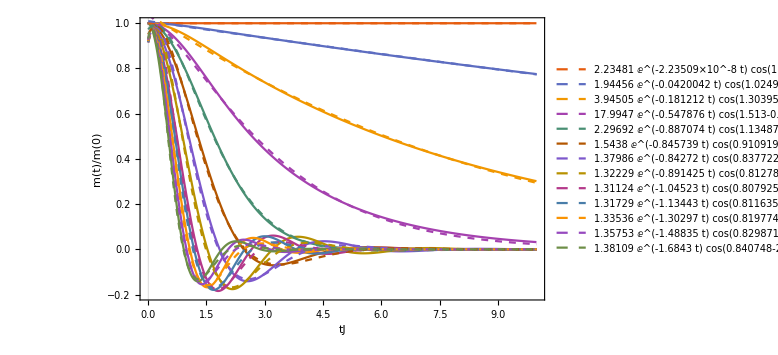

```mathematica
Jrescale=5;
flist={{-0.4,0.2,0.2},{-0.35,0.15,0.2},{-0.3,0.1,0.2},{-0.25,0.05,0.2},{-0.2,0.0,0.2},{-0.15,-0.05,0.2},{-0.1,-0.1,0.2},{-0.05,-0.15,0.2},{0.02,-0.22,0.2},{0.05,-0.25,0.2},{0.1,-0.3,0.2},{0.15,-0.35,0.2},{0.2,-0.4,0.2}}*Jrescale;
(*hlist={0.05,0.2,0.5,1.0,5.0,10.0};
hlist={0.08,0.1,0.15,0.25};*)
hlist=Table[10.0,{i,1,Length[flist]}];
Tlist=hlist/0.4;
fontsize=14;
setlen=Length[hlist];

fitSxfreqDecaylist=Table[SxHamfixhJSpinSetsHighLowExpDraftVersion[flist,Tlist,hlist,"0_0",Table[2001,{i,1,setlen}],Table[3000,{i,1,setlen}],"dynamics_20230715_draftRandomf_hightemp_SpinModel_Jbar0_rhox",False,2000,1,-0.2,All,0,10.0,fontsize,False,1,j];Thread[{omegalist,decaylist}],{j,500,1200,50}]


(*For Plot*)
SxWormholeJbar0HighTempDraft=SxHamfixhJSpinSetsHighLowExpDraftVersion[flist,Tlist,hlist,"0_0",Table[2001,{i,1,setlen}],Table[3000,{i,1,setlen}],"dynamics_20230715_draftRandomf_hightemp_SpinModel_Jbar0_rhox",False,2000,1,-0.2,All,0,10.0,fontsize,False,1,1000]
```

```mathematica
fitSxfreqlist//Dimensions
```

{15,12}

```mathematica
Mean[fitSxfreqlist]
```

{6.33351×10^-7,0.0152918,0.0223862,0.0276638,0.532255,0.993365,1.32557,1.60195,1.93767,2.06985,2.27858,2.47633}

```mathematica
Min[fitSxfreqlist[[;;,1]]]
```

7.33753×10^-9

```mathematica
fitSxfreqlist[[;;,1]]
```

{1.06563×10^-7,3.77919×10^-8,4.39045×10^-8,4.01131×10^-8,7.33753×10^-9,2.01809×10^-7,6.71382×10^-7,2.56993×10^-6,6.82582×10^-7,3.19174×10^-7,1.0979×10^-6,3.65399×10^-6,1.36882×10^-8,8.90849×10^-9,4.51951×10^-8}

{1.31.31.310^-7,0.00310.00150.0015,0.00450.00170.0017,0.00550.00120.0012,0.10650.00040.0004,0.19870.00100.0010,0.26510.00070.0007,0.32040.00120.0012,0.387530.000240.00024,0.413970.000230.00023,0.455720.000080.00008,0.49526788,0.53313403434}

{1.71.71.710^-7,0.00920.00150.0015,0.0390.0040.004,0.11150.00280.0028,0.1770.0070.007,0.16970.00100.0010,0.16870.00060.0006,0.17830.00040.0004,0.209030.000130.00013,0.226940.000170.00017,0.2608780.0000290.000029,0.29832499,0.33801955}

{a→0.74400.00060.0006}

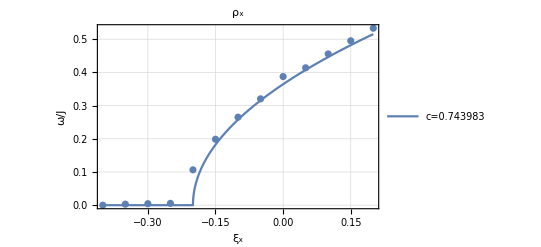

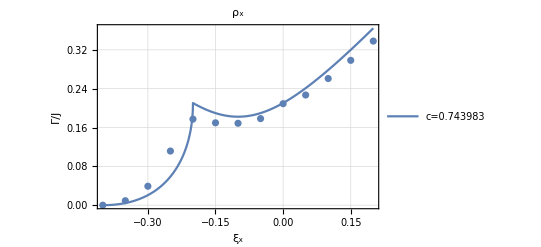

```mathematica
(*Prepare Data*)
fitSxfreqlist=fitSxfreqDecaylist[[;;,;;,1]];
fitSxDecaylist=fitSxfreqDecaylist[[;;,;;,2]];
statData=Table[{Mean[fitSxfreqlist[[;;,i]]],Min[fitSxfreqlist[[;;,i]]],Max[fitSxfreqlist[[;;,i]]]},{i,1,Length[flist]}];
(*After J rescale*)
dataFreqLargeNplot=Table[Around[statData[[i,1]],{statData[[i,2]]-statData[[i,1]],statData[[i,3]]-statData[[i,1]]}],{i,1,Length[flist]}]/Jrescale
statData=Table[{Mean[fitSxDecaylist[[;;,i]]],Min[fitSxDecaylist[[;;,i]]],Max[fitSxDecaylist[[;;,i]]]},{i,1,Length[flist]}];
dataDecayLargeNplot=Table[Around[statData[[i,1]],{statData[[i,2]]-statData[[i,1]],statData[[i,3]]-statData[[i,1]]}],{i,1,Length[flist]}]/Jrescale
(*Plot*)
Jrescale=5.0;
xilist=flist/Jrescale;
xixarr=xilist[[;;,1]];
freqtheory=Table[√(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2)/.{ξ1->xilist[[i,1]],ξ2->xilist[[i,2]],ξ3->xilist[[i,3]]},{i,1,Length[xilist]}]//N//Re;
Bpoly=(If[(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2)>0,√(ξ1^2+ξ2^2+ξ3^2),√(ξ1^2+ξ2^2+ξ3^2)-√(-(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2))]);
decaytheory=Table[Bpoly/.{ξ1->xilist[[i,1]],ξ2->xilist[[i,2]],ξ3->xilist[[i,3]]},{i,1,Length[xilist]}]//N//Re;
(*freqtheoryLargeNresult=FindFit[Thread[{freqtheory,dataFreqLargeNplot}],a x,{a},x]
decaytheoryLargeNresult=FindFit[Thread[{decaytheory,dataDecayLargeNplot}],a x,{a},x]*)
fitLargeNresult=FindFit[Thread[{Join[freqtheory,decaytheory],Join[dataFreqLargeNplot,dataDecayLargeNplot]}],a x,{a},x]

Show[Plot[{((a/.fitLargeNresult)[[1]])*(√(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2)/.{ξ1->x,ξ2->-0.2-x,ξ3->0.2})//N//Re},{x,-0.4,0.2},PlotTheme->"Detailed",PlotLegends->{"c="<>ToString[((a/.fitLargeNresult)[[1]])]},PlotPoints->400]
,ListPlot[{Thread[{xixarr,dataFreqLargeNplot}]},PlotTheme->"Detailed"],PlotRange->All,PlotLabel->"ρ_x",FrameLabel->{"ξ_x","ω/J"}]
Show[Plot[{((a/.fitLargeNresult)[[1]])*(Bpoly/.{ξ1->x,ξ2->-0.2-x,ξ3->0.2})//N//Re},{x,-0.4,0.2},PlotTheme->"Detailed",PlotLegends->{"c="<>ToString[((a/.fitLargeNresult)[[1]])]},PlotPoints->400]
,ListPlot[{Thread[{xixarr,dataDecayLargeNplot}]},PlotTheme->"Detailed"],PlotRange->All,PlotLabel->"ρ_x",FrameLabel->{"ξ_x","Γ/J"}]
```

```mathematica
Export[FileNameJoin[{"C:\\Users\\tgzhou\\Dropbox\\Project\\NMR_wormhole\\draft\\Universal Aspect of Relaxation Dynamics in Random Spin Models\\supp","flist.xlsx"}],{dataplot,dataEDplot,Sxfreqtheory}]
```

C:\Users\tgzhou\Dropbox\Project\NMR_wormhole\draft\Universal Aspect of Relaxation Dynamics in Random Spin Models\supp\flist.xlsx

```mathematica
{dataplot[[1;;19]][[;;,1]],dataplot[[1;;19]][[;;,2]],dataEDplot[[;;,1]],dataEDplot[[;;,2]],Sxfreqtheory}//TableForm
```

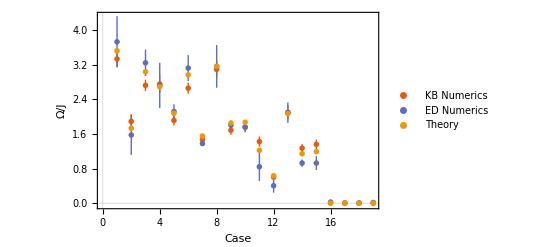

```mathematica
fontsize=14;
figFreqNumerics=ListPlot[{dataplot,dataEDplot,Sxfreqtheory}[[;;,1;;19]],PlotLegends->Placed[PointLegend[{"KB Numerics","ED Numerics","Theory"},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.81,0.78}],PlotTheme->"Scientific",FrameLabel->{"Case","Ω/J"},BaseStyle->fontsize,PlotMarkers->"OpenMarkers",LabelStyle->{fontsize,GrayLevel[0]}]
```

```mathematica
Export[FileNameJoin[{"C:\\Users\\tgzhou\\Dropbox\\Project\\NMR_wormhole\\draft\\Universal Aspect of Relaxation Dynamics in Random Spin Models","figFreqNumerics.pdf"}],figFreqNumerics]
```

C:\Users\tgzhou\Dropbox\Project\NMR_wormhole\draft\Universal Aspect of Relaxation Dynamics in Random Spin Models\figFreqNumerics.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\tgzhou\\Research\\Project\\ongoing_project\\NMR_wormhole\\julia\\LargeN_dynamics_anyfhighT\\figFreqNumerics.pdf"]]]
```

```mathematica
Around[1.0,{-1.0,0.5}]
```

1.01.00.5